```mathematica
data={{24,24,5},{24,96,6},{24,120,7},{24,288,8},{24,504,9},{24,1056,10},{24,2040,11},{96,72,8},{96,96,7},{96,120,7},{96,216,9},{96,264,10},{96,384,9},{96,480,10},{96,600,11},{96,1152,11},{120,72,8},{120,96,11},{120,120,8},{120,144,9},{120,168,10},{120,192,11},{120,216,9},{120,240,11},{120,288,8},{120,312,12},{120,336,11},{120,360,12},{120,384,11},{120,408,11},{120,480,10},{120,504,12},{120,576,12},{120,600,11},{120,672,10},{120,888,12},{120,984,11},{72,48,9},{72,72,9},{72,120,10},{72,144,9},{72,216,9}
,{72,288,11},{72,312,10},{72,336,10},{72,360,12},{72,528,11},{72,696,11},{72,1080,12},{72,1296,12},{288,168,10},{288,192,12},{288,216,9},{288,264,10},{288,288,9},{288,312,11},{288,360,12},{288,504,9},{288,576,12},{288,864,12},{288,984,11},{288,1152,11},{288,1440,12},{216,120,10},{216,168,10},{216,192,11},{216,216,10},{216,240,11},{216,264,10},{216,336,10},{216,408,12},{216,504,12},{216,528,11},{216,552,12},{216,576,12},{216,648,12},{216,672,10},{216,696,11},{216,720,12},{216,864,12},{216,1824,12},{384,240,11},{384,288,11},{384,336,10},{384,384,10},{384,480,10},{384,528,12},{384,864,12},{384,1536,12},{144,96,11},{144,120,10},{144,144,10},{144,168,10},{144,192,11},{144,240,11},{144,264,11},{144,312,10},{144,336,10},{144,384,11},{144,408,11},{144,456,12},{144,504,12},{144,576,12},{144,768,12},{144,792,12},{144,960,11},{144,1488,12},{504,264,10},{504,336,11},{504,504,10},{504,600,11},{504,1056,10},{48,48,10},{48,120,10},{48,144,10},{48,192,10},{48,216,11},{48,240,11},{48,384,11},{48,408,12},{48,624,12},{264,144,11},{264,216,12},{264,240,11},{264,264,11},{264,336,11},{264,408,12},{264,528,12},{264,600,11},{264,984,11},{264,1080,12},{264,1296,12},{480,264,11},{480,288,11},{480,360,12},{480,480,11},{480,552,12},{480,576,12},{480,600,11},{480,696,12},{480,864,12},{480,1152,11},{168,96,11},{168,144,11},{168,168,11},{168,192,11},{168,264,11},{168,312,11},{168,336,11},{168,360,12},{168,384,12},{168,408,12},{168,504,12},{168,528,11},{168,696,11},{168,720,12},{168,792,12},{168,1488,12},{3 12,168,11},{312,216,11},{312,264,11},{312,288,12},{312,312,11},{312,360,12},{312,384,11},{312,408,11},{312,528,11},{312,576,12},{312,912,12},{312,1440,12},{336,192,12},{336,216,11},{336,240,11},{336,264,11},{336,336,11},{336,360,12},{336,504,12},{336,672,12},{336,696,11},{336,912,12},{336,960,11},{672,360,12},{672,408,11},{672,456,12},{672,552,12},{672,672,11},{672,696,11},{672,984,11},{192,168,11},{192,192,11},{192,240,11},{1056,600,11},{1056,1056,11},{1056,2040,11},{240,168,12},{240,192,12},{2 40,240,12},{240,408,12},{240,528,12},{240,552,12},{240,672,12},{600,360,12},{600,384,12},{600,456,12},{600,600,12},{600,1440,12}
};Print[ToString[Length[data]]<> " entries."]
```

206 entries.

```mathematica
connections=Map[#[[1]]->#[[2]]&,data];Print["ok"]
```

ok

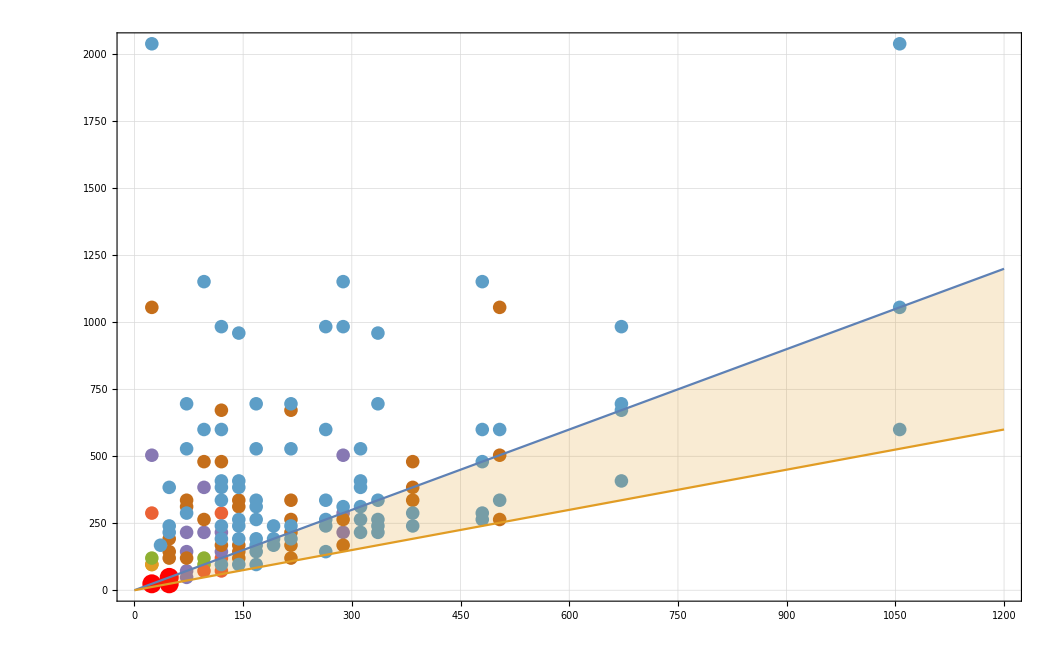

```mathematica
Show[

ListPlot[Table[Map[Tooltip[{#[[1]],#[[2]]},{ {#[[1]]->#[[2]]},#[[3]]}]&, Select[data,#[[3]]==k&]],{k,5,11}],ColorFunction->ColorData[3,"ColorList"]],
ListPlot[{{24,24},{48,24},{48,48}}, PlotStyle->Red],
Plot[{x,x/2},{x,0,1200},  Filling->{2->{1}}], 
Frame->True, GridLines->Automatic, PlotRange->All
]
```